### Mean clusters

Note: Repeatedly crashing my computer: SW should try

```mathematica
pcas = With[{ru={299459058088077823758143088095350287424,4,1}},PerturbedCellularAutomaton[ru, {{1}, 0}, {120, {-30, 50}}, #, "ReturnPerturbations"->False]&/@ allperts[CellularAutomaton[ru, {{1}, 0}, {120, {-30, 50}}]]];
```

```mathematica
SeedRandom[4445];
out = FindClusters[PlotCA[pcas[[#]], "Trim"->{None, None}]->#&/@ RandomSample[Range[Length[pcas]], 3]]
```

{{3562},{4145},{1181}}

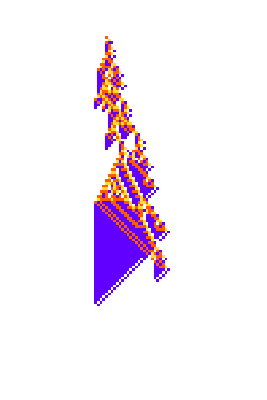
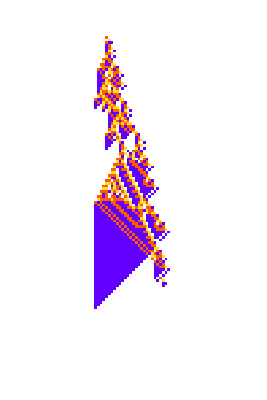
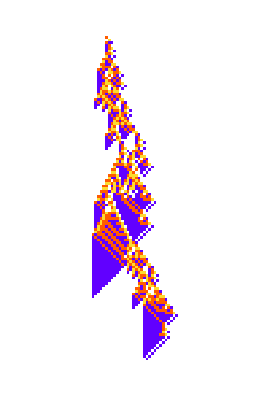

```mathematica
ArrayPlot[Map[Blend[Take[Last/@colorrules,4],BinCounts[#,{0,4,1}]]&,Transpose[pcas[[#]],{3,1,2}],{2}]]&/@ out
```

## The Effect of Genetic Diversity

Modernized Histogram code to run

Overall effect on lifetime:

```mathematica
poplts = 
Module[
{ru = {299459058088077823758143088095350287424,4,1},init = {{1}, 0}, txspec = {400, {-110, 110}},ca, aps},
SeedRandom[5555];
ParallelMap[Function[rule, 
ca = CellularAutomaton[rule, init, txspec];
aps = allperts[ca, 4];
TestCALifeTime[PerturbedCellularAutomaton[rule, init, txspec, #]]&/@ aps],RandomSample[quickneutral[ru], 1]]]
```

{{0,1,100,1,102,2,4,5,20,3,45,99,101,8,12,104,20,104,4,5,47,16,99,105,7,18,12,102,15,13,16,11,25,6,104,8,25,18,104,49,65,85,18,103,107,9,16,149,23,140,49,9,17,10,107,18,27,22,103,51,142,24,107,51,21,150,15,16,113,103,51,59,142,63,27,20,110,21,34,35,70,26,65,59,30,24,35,62,150,49,20,22,55,55,42,54,111,33,68,63,36,74,26,30,115,143,49,150,109,34,48,159,119,65,40,28,32,33,28,52,37,23,23,32,32,24,23,23,126,47,42,53,33,33,26,82,117,114,28,28,28,20,35,26,82,29,110,138,138,25,47,93,61,23,23,119,58,38,72,33,50,25,39,117,110,138,31,28,61,35,28,82,29,32,337,73,49,47,101,60,30,35,175,23,26,38,76,28,33,24,31,33,46,39,44,144,27,138,164,51,51,144,101,63,97,169,125,47,163,43,58,101,32,31,39,35,38,35,27,28,39,48,40,115,41,101,117,135,140,140,105,97,66,73,47,39,62,47,163,134,61,27,183,32,39,33,37,136,31,101,36,123,164,164,110,84,141,110,140,140,49,47,85,123,47,39,94,163,129,60,44,34,64,43,125,40,92,60,60,92,47,133,164,164,46,156,45,133,171,179,132,47,173,90,173,85,138,163,123,39,128,66,42,89,62,42,170,47,53,124,46,208,97,133,92,44,144,164,45,156,130,44,101,73,47,101,46,173,131,46,46,35,44,164,66,74,177,59,59,116,147,62,36,103,53,97,124,72,46,156,133,44,155,134,47,50,72,148,123,123,153,65,131,189,286,40,56,131,93,40,107,81,62,90,42,76,96,73,48,111,81,47,136,47,110,64,53,101,57,110,131,131,52,50,131,50,81,81,219,49,71,129,73,194,42,74,75,194,68,94,175,46,144,46,125,123,69,101,57,72,131,131,183,131,131,47,48,81,128,71,126,153,46,55,65,145,147,309,101,74,74,141,40,107,57,47,57,91,143,66,101,48,175,131,131,127,67,103,60,48,81,103,75,75,101,101,75,233,46,55,146,55,247,133,74,101,74,55,153,44,46,61,46,69,167,133,42,132,42,131,136,184,98,49,78,169,169,276,42,75,50,101,170,107,135,170,138,55,287,55,107,76,62,46,91,148,110,51,50,54,44,133,66,81,42,48,49,56,128,136,56,44,124,52,169,40,118,101,135,179,170,101,93,81,101,68,107,46,111,57,50,164,74,126,74,58,97,55,211,48,42,49,40,67,44,40,40,55,60,131,42,172,124,148,135,67,55,101,188,46,107,57,46,65,58,73,64,69,42,86,187,46,54,75,67,42,44,91,40,50,68,57,131,86,76,94,113,102,134,46,57,93,62,244,144,101,70,104,54,132,64,191,44,44,38,167,36,184,69,67,131,64,113,100,155,64,46,57,139,196,64,73,70,63,41,42,99,47,63,102,68,54,66,50,202,101,53,86,44,63,100,67,135,100,196,130,46,57,149,97,53,191,58,149,146,68,151,68,57,221,62,86,89,167,100,135,230,155,67,58,188,135,196,156,149,57,101,110,144,146,195,102,141,134,62,177,139,86,100,103,135,135,79,135,120,65,45,65,97,56,152,208,166,202,139,202,119,77,71,70,202,65,55,80,167,100,189,143,135,70,135,340,75,135,97,72,80,96,103,77,106,202,147,73,202,123,71,71,89,45,45,109,134,70,91,76,89,150,65,173,100,110,201,89,72,60,118,340,77,146,96,61,77,55,202,71,202,202,70,94,71,47,45,134,53,145,76,70,68,128,137,135,121,147,363,73,340,96,146,167,149,61,63,147,61,56,106,202,57,90,73,160,94,71,73,54,102,138,66,67,92,101,174,125,71,71,67,135,160,132,135,135,135,149,90,135,147,114,364,106,98,82,166,61,48,202,122,149,346,57,104,138,138,114,80,66,138,101,235,116,66,67,118,193,68,83,71,101,68,69,81,135,135,231,147,106,96,80,166,44,97,98,104,53,101,70,85,138,102,56,117,109,88,138,138,177,101,139,139,101,99,117,67,68,120,145,71,154,135,81,71,115,65,72,166,135,59,93,104,151,145,101,199,101,102,77,136,102,111,138,162,333,138,287,138,136,138,138,101,95,95,101,139,77,101,99,65,68,67,162,82,67,128,135,135,104,164,55,104,85,101,163,165,66,93,101,102,145,80,102,167,138,144,86,138,80,138,141,174,88,204,231,144,101,195,192,101,95,133,139,101,67,101,67,186,64,67,242,69,94,58,135,135,83,80,66,135,146,94,121,138,187,96,86,102,88,117,80,180,138,138,137,89,85,204,101,100,199,195,101,100,104,101,67,101,67,74,96,67,157,70,78,164,61,192,175,94,160,185,74,117,73,156,186,351,138,187,88,138,108,138,180,174,144,77,141,91,85,204,171,70,87,84,89,97,63,190,296,58,84,105,81,113,113,84,156,152,81,156,113,187,141,210,92,85,98,144,86,98,220,162,70,144,77,81,71,80,81,95,129,76,220,127,106,152,203,176,79,74,183,92,221,162,109,67,164,67,71,67,174,78,153,174,114,110,81,136,173,94,89,271,220,144,176,83,197,187,155,105,110,97,88,126,119,121,139,90,100,70,76,139,92,98,123,145,174,174,138,131,185,187,101,144,86,105,87,149,184,99,183,96,240,101,182,121,105,163,86,103,101,112,141,139,65,76,139,112,110,73,114,85,133,94,131,169,112,110,134,79,138,95,111,86,106,101,101,157,99,85,136,89,-∞,304,83,83,159,121,139,139,118,139,139,101,139,108,146,164,190,89,97,92,315,135,92,110,169,197,101,110,160,138,91,79,100,87,98,202,101,175,96,85,85,87,94,252,243,110,235,139,139,139,139,155,95,98,108,93,117,145,93,178,87,78,209,169,166,165,165,137,111,101,91,107,110,110,97,91,263,83,87,131,101,92,202,89,100,85,98,101,167,144,101,144,139,218,151,124,139,181,98,94,199,253,116,195,152,146,162,180,123,217,112,92,165,107,137,190,107,100,201,118,101,187,96,110,234,91,91,213,89,87,83,92,101,113,144,89,171,124,108,130,222,112,171,183,98,184,171,171,159,199,195,164,123,123,146,93,166,107,107,187,137,104,101,95,121,135,227,125,101,150,101,110,118,91,89,92,144,131,85,130,103,121,208,198,121,94,181,171,146,164,171,199,243,164,133,150,194,195,169,169,100,181,205,180,165,104,121,102,101,117,167,136,165,135,182,77,101,165,115,110,224,89,144,92,102,103,103,98,121,105,227,90,118,199,138,103,232,150,108,183,183,96,114,116,224,181,92,169,96,170,121,117,128,177,165,165,177,83,224,190,78,135,102,344,207,186,100,110,101,96,131,287,187,109,103,103,100,103,120,105,106,97,118,118,104,147,119,146,224,183,114,268,224,154,144,169,116,191,178,100,117,171,83,104,165,83,164,190,78,95,93,93,224,224,135,115,128,101,101,92,223,128,101,185,96,98,172,81,154,106,122,176,132,97,106,210,118,120,184,126,138,194,147,108,124,144,108,202,202,103,130,161,238,117,219,191,83,104,93,78,95,111,104,101,175,100,101,143,138,101,224,126,115,122,87,101,206,101,101,124,197,105,103,165,121,171,103,101,130,185,121,182,111,120,120,101,117,204,164,377,340,90,238,202,130,166,133,105,129,107,161,129,101,177,111,102,197,165,104,100,175,101,138,110,105,96,101,101,200,101,114,128,115,186,157,101,121,157,96,101,165,151,118,165,104,101,117,178,141,182,343,186,182,101,182,98,85,166,155,79,166,133,215,155,167,129,193,218,218,149,117,219,95,111,133,129,100,219,90,138,90,99,165,91,115,99,96,118,114,97,97,144,96,254,131,101,93,96,93,93,128,101,128,118,106,118,105,106,110,169,178,187,198,128,124,115,117,115,133,83,97,101,112,128,101,168,232,146,155,86,193,114,218,117,103,110,268,140,104,219,162,188,93,98,-∞,112,104,165,99,135,190,114,101,114,144,96,179,131,97,93,96,93,188,128,101,128,105,103,106,144,396,193,158,119,193,169,186,187,133,115,118,183,109,168,185,166,168,255,167,117,175,99,101,100,146,127,103,140,193,207,207,152,125,143,292,98,151,162,89,97,113,114,119,215,144,101,165,131,197,93,96,93,218,128,101,128,106,107,129,105,178,114,193,187,211,362,218,124,115,115,101,100,112,178,166,101,101,117,182,168,101,120,128,101,89,90,103,245,98,125,117,207,125,94,134,161,138,170,143,198,157,177,145,98,183,165,93,131,91,93,116,93,193,128,105,106,118,186,107,102,114,239,220,205,115,354,115,101,112,279,101,194,101,101,182,117,101,121,152,101,89,89,101,264,105,250,104,142,101,135,99,136,100,138,186,172,114,168,106,253,107,145,140,198,105,165,190,93,97,162,128,147,106,150,151,122,100,143,155,115,115,127,107,180,203,101,101,117,162,101,115,101,101,118,106,101,112,117,101,165,101,101,141,116,101,97,89,89,89,100,141,107,97,213,172,106,168,172,162,217,156,253,119,253,158,157,134,99,116,95,119,114,128,100,123,141,150,151,154,122,151,354,115,115,208,169,180,264,101,101,107,109,101,115,101,101,117,167,101,101,107,101,117,101,101,157,165,104,101,141,327,89,168,101,135,162,91,186,92,265,145,162,90,151,129,243,136,116,104,123,98,95,101,108,144,180,100,122,121,100,122,192,150,151,158,122,151,157,115,115,121,117,180,206,101,101,168,118,101,115,101,101,145,116,101,165,165,101,156,263,101,250,104,127,182,183,175,137,100,172,101,99,182,219,145,105,129,146,243,89,116,99,226,104,173,116,141,108,95,180,120,143,100,105,111,100,122,153,100,122,201,150,151,150,122,151,204,115,115,127,107,180,148,101,101,117,109,101,115,101,101,177,106,101,109,117,101,109,101,89,263,107,101,127,172,172,104,213,172,138,219,219,89,166,182,143,100,109,109,181,114,114,105,172,95,98,188,110,100,106,154,100,105,126,100,122,156,100,122,228,150,151,202,122,151,157,115,115,151,168,180,126,101,101,107,118,101,115,101,101,117,166,101,98,107,101,107,101,89,148,109,101,124,172,172,172,92,101,104,112,219,107,182,112,96,107,193,136,136,153,134,172,130,109,97,111,104,100,106,117,100,106,122,100,105,126,100,122,102,100,122,168,150,151,219,122,151,204,115,115,115,117,180,126,101,101,167,109,101,115,101,101,270,116,101,99,109,101,109,101,89,107,105,101,100,107,172,101,219,109,213,132,114,97,107,104,128,160,101,136,100,110,179,109,152,173,99,193,93,100,107,123,100,106,218,100,106,116,100,105,103,100,122,145,100,122,232,150,151,157,122,151,157,115,115,160,107,180,145,101,101,117,118,101,115,101,101,107,106,101,96,107,101,122,101,89,107,113,219,92,107,172,157,124,97,151,113,128,101,135,180,161,127,101,104,107,110,136,152,99,97,100,106,199,100,107,121,100,106,131,100,106,176,100,105,115,100,122,111,100,122,230,150,151,238,122,151,204,115,115,140,167,180,153,101,101,107,109,101,115,101,101,131,165,101,107,343,101,101,89,89,96,138,121,139,100,152,113,135,119,107,108,222,185,117,180,207,123,137,108,141,110,124,104,147,103,100,107,114,100,106,116,100,107,125,100,106,115,100,106,113,100,105,103,100,122,102,100,122,266,150,151,119,122,151,157,115,115,123,117,180,159,101,101,166,115,101,115,101,101,220,116,101,142,115,101,108,121,155,89,107,151,114,108,93,153,117,117,193,177,184,136,180,105,178,124,101,149,115,154,124,144,104,110,100,106,123,100,107,158,100,106,121,100,107,113,100,106,103,100,106,176,100,105,115,100,122,144,100,122,111,150,151,195,122,151,204,115,115,132,107,180,157,101,101,117,123,101,92,104,101,257,185,101,115,238,101,165,219,103,111,100,115,117,93,193,111,184,213,111,103,101,184,105,126,109,123,124,149,124,124,124,100,107,158,100,106,162,100,107,117,100,106,103,100,107,176,100,106,115,100,106,113,100,105,103,100,122,111,100,122,189,150,151,295,122,151,157,115,115,148,166,180,127,101,101,110,117,101,93,101,101,104,107,165,184,94,114,101,93,178,107,112,213,220,103,107,112,97,101,245,146,101,218,101,126,227,221,124,124,157,111,176,100,106,117,100,107,176,100,106,246,100,107,176,100,106,115,100,107,113,100,106,103,100,106,176,100,105,115,100,122,102,100,122,160,150,151,111,122,151,204,115,115,111,117,180,187,101,101,130,107,101,107,160,101,185,165,101,97,169,105,222,100,117,103,97,112,111,125,126,105,114,207,103,160,111,180,143,148,342,111,123,271,101,101,101,100,107,126,100,106,131,100,107,207,100,106,115,100,107,113,100,106,103,100,107,176,100,106,115,100,106,113,100,105,103,100,122,143,100,122,203,150,151,179,122,151,257,115,115,131,107,180,161,101,101,101,165,101,185,101,108,160,105,179,101,97,178,98,125,114,176,114,107,230,160,109,240,143,207,214,111,123,127,101,101,101,100,106,125,100,107,123,100,106,133,100,107,113,100,106,103,100,107,176,100,106,115,100,107,113,100,106,103,100,106,176,100,105,115,100,122,111,100,122,139,150,151,134,122,151,238,115,115,177,165,180,108,101,101,107,238,101,114,108,108,102,174,99,116,100,103,114,160,150,109,143,114,178,109,123,128,101,101,101,100,107,133,100,106,127,100,107,188,100,106,103,100,107,176,100,106,115,100,107,113,100,106,103,100,107,176,100,106,115,100,106,113,100,105,103,100,122,102,100,122,254,150,151,134,122,151,123,115,115,145,117,180,238,101,101,189,107,180,115,99,107,108,99,109,101,179,141,102,107,123,119,101,119,113,100,106,121,100,107,157,100,106,198,100,107,176,100,106,115,100,107,113,100,106,103,100,107,176,100,106,115,100,107,113,100,106,103,100,106,176,100,105,115,100,122,225,100,122,131,150,151,190,122,151,165,115,115,228,107,180,131,116,101,178,180,108,118,106,180,141,99,112,105,100,107,125,100,106,137,100,107,146,100,106,115,100,107,113,100,106,103,100,107,176,100,106,115,100,107,113,100,106,103,100,107,176,100,106,115,100,106,113,100,105,103,100,122,135,100,122,150,150,151,126,122,151,125,115,115,103,109,180,201,232,101,116,107,108,115,180,182,106,100,106,124,100,107,123,100,106,251,100,107,113,100,106,103,100,107,176,100,106,115,100,107,113,100,106,103,100,107,176,100,106,115,100,107,113,100,106,103,100,106,176,100,105,149,100,122,102,100,122,170,150,151,165,122,151,153,115,115,97,117,180,146,118,261,232,102,108,126,155,117,183,100,107,162,100,106,143,100,107,112,100,106,103,100,107,176,100,106,115,100,107,113,100,106,103,100,107,176,100,106,115,100,107,113,100,106,103,100,107,176,100,106,115,100,106,113,100,105,103,100,122,123,100,122,159,150,151,217,118,151,119,115,115,99,180,186,127,113,115,224,180,106,103,133,101,103,100,106,197,100,107,123,100,106,187,100,107,176,100,106,115,100,107,113,100,106,103,100,107,176,100,106,115,100,107,113,100,106,103,100,107,176,100,106,115,100,107,113,100,106,103,100,106,138,100,105,123,100,122,111,100,122,213,150,151,164,125,263,135,115,115,115,112,135,101,136,110,184,126,126,101,100,107,133,100,106,118,100,107,190,100,106,115,100,107,113,100,106,103,100,107,176,100,106,115,100,107,113,100,106,103,100,107,176,100,106,115,100,107,113,100,106,103,100,107,176,100,106,149,100,106,113,100,105,103,100,122,139,160,122,191,151,139,116,101,177,127,104,101,101,107,101,101,136,101,101,101,115,161,100,106,123,100,107,145,100,106,106,100,107,113,100,106,103,100,107,176,100,106,115,100,107,113,100,106,103,100,107,176,100,106,115,100,107,113,100,106,103,100,107,176,100,106,115,100,107,113,100,106,103,100,106,124,100,105,168,122,111,123,171,112,123,101,101,101,119,101,228,183,101,126,101,226,101,101,101,113,101,101,101,100,107,132,100,106,139,100,107,194,100,106,103,100,107,176,100,106,115,100,107,113,100,106,103,100,107,176,100,106,115,100,107,113,100,106,103,100,107,176,100,106,115,100,107,113,100,106,103,100,107,153,100,106,118,106,102,112,102,102,101,101,101,101,101,101,101,101,101,101,101,176,188,101,101,101,101,184,165,100,106,122,100,107,134,100,106,195,100,107,186,100,106,115,100,107,113,100,106,103,100,107,176,100,106,115,100,107,113,100,106,103,100,107,176,100,106,115,100,107,113,100,106,103,100,107,116,100,106,112,107,102,121,102,102,101,194,101,189,101,101,101,101,101,151,101,101,107,101,101,106,150,101,156,101,101,101,100,107,137,100,106,260,100,107,221,100,106,115,100,107,113,100,106,103,100,107,176,100,106,115,100,107,113,100,106,103,100,107,176,100,106,115,100,107,113,100,106,103,100,107,116,100,106,112,107,102,113,102,102,101,189,101,153,185,101,189,101,101,194,101,101,133,101,101,138,192,101,232,101,101,103,101,101,157,101,101,101,100,106,131,100,107,152,100,106,117,100,107,113,100,106,103,100,107,176,100,106,115,100,107,113,100,106,103,100,107,176,100,106,115,100,107,113,100,106,103,100,107,116,100,106,112,107,102,113,102,102,101,187,101,186,189,101,186,101,101,189,101,101,185,101,101,108,101,101,182,101,101,101,101,101,108,101,101,101,101,101,123,101,101,101,100,107,127,100,106,155,100,107,110,100,106,103,100,107,186,100,106,115,100,107,113,100,106,103,100,107,176,100,106,115,100,107,113,100,106,103,100,107,116,100,106,112,107,102,113,102,102,101,188,101,187,188,101,187,189,101,187,105,101,189,101,101,101,101,101,183,101,187,105,101,101,193,101,101,101,101,101,103,101,101,101,100,106,123,100,107,143,100,106,119,100,107,209,100,106,115,100,107,113,100,106,103,100,107,176,100,106,115,100,107,113,100,106,103,100,107,116,100,106,112,107,102,113,102,102,101,189,101,188,189,101,188,189,101,188,189,101,188,188,101,189,101,101,105,188,101,106,101,101,182,101,187,184,101,101,161,101,101,101,100,107,252,100,106,193,100,107,109,100,106,115,100,107,113,100,106,103,100,107,176,100,106,115,100,107,113,100,106,103,100,107,116,100,106,112,107,102,113,102,102,101,190,101,189,190,101,189,190,101,189,190,101,189,190,101,189,190,101,189,101,101,188,101,101,183,101,101,101,101,101,142,101,101,101,100,106,213,100,107,174,100,106,161,100,107,113,100,106,103,100,107,186,100,106,115,100,107,113,100,106,103,100,107,116,100,106,112,107,102,113,102,102,101,191,101,190,191,101,190,191,101,190,191,101,190,191,101,190,191,101,190,191,101,190,191,101,190,101,101,101,189,101,225,101,191,190,100,107,139,100,106,147,100,107,241,100,106,103,100,107,209,100,106,115,100,107,113,100,106,103,100,107,116,100,106,112,100,106,194,100,107,192,100,106,122,100,107,210,100,106,115,100,107,113,100,106,103,100,107,116,100,106,112,100,107,204,100,106,141,100,107,150,100,106,115,100,107,113,100,106,103,100,107,116,100,106,112,100,106,152,100,107,107,100,106,122,100,107,113,100,106,103,100,107,116,100,106,112,100,107,257,100,106,114,100,107,177,100,106,103,100,107,132,100,106,112,100,106,118,100,107,103,100,106,194,100,107,112,100,106,112,100,107,193,100,106,110,100,107,170,100,106,112,100,197,116,100,107,151,100,106,112,100,198,234,100,197,143,100,201,200}}

```mathematica
Histogram[#, 100, "Probability",AspectRatio->.4]&/@ poplts //GraphicsGrid[Partition[#,5]]&
```

[[[ same analyses; different genomes ]]]

[[ Therapy that works on one genome doesn’t necessarily work on others .... show all 64 cases ]]

## Biological Evolution and Our Model Organism

[[ Could be whole organism, or could be e.g. an organ ]]

```mathematica
rh = Reap[mh = Module[{ru,ca,lt,lts, pcas,fitness, initru = {0,4,1}, initfit = {0}},SeedRandom[7899623];
Sow[{initru,{<||>}, initfit}];
NestList[CompoundExpression[
ru=RandomRuleMutation[First[#]],
ca=CellularAutomaton[ru,{{1},0},{200,{-200,200}}];
lt=TestCALifeTime[ca];
If[lt==-Infinity,Sow[{ru, <||>,{lt}}];#,
pcas=Table[PerturbedCellularAutomaton[ru,{{1},0},{200,{-200,200}},1],Ceiling[lt/10]];
fitness=Min[lts = Join[{lt},TestCALifeTime/@(First/@pcas)]];
Sow[{ru, Last/@pcas,lts}];
If[fitness>=Last[#],{ru,fitness},#]]]&,{initru, First[initfit]},2000]]][[2, 1]];
```

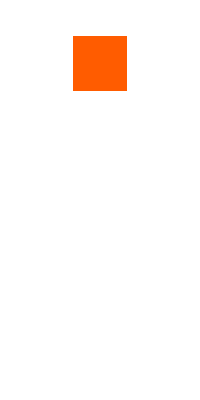
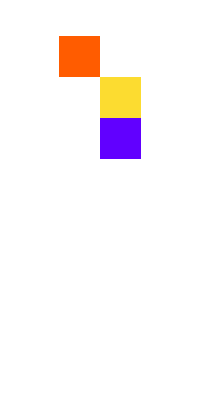
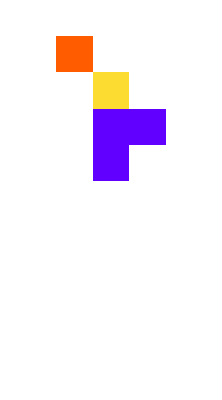
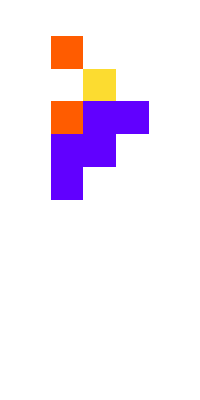
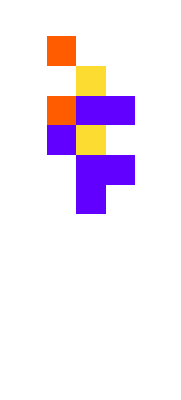
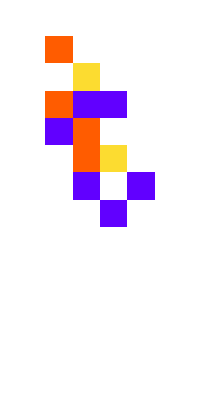
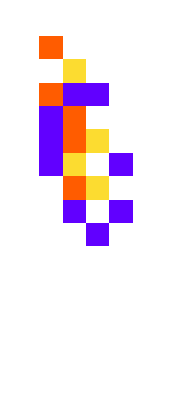
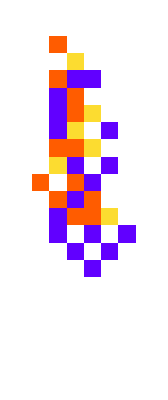
{-Graphics-0,-Graphics-1,-Graphics-2,-Graphics-3,-Graphics-4,-Graphics-5,-Graphics-6,-Graphics-7,-Graphics-9,-Graphics-12,-Graphics-14,-Graphics-15,-Graphics-37,-Graphics-38,-Graphics-40,-Graphics-49,-Graphics-60,-Graphics-68,-Graphics-84,-Graphics-101}

```mathematica
Labeled[PlotCA[First[#],"Trim"->{1,5},ImageSize->{Automatic,25 Sqrt[1+Last[#]]}],Text[Style[Last[#],Small]]]&/@(First/@SplitBy[mh,Last])
```

#### All perturbations

```mathematica
Join@@<||>
```

{}

```mathematica
rh[[Rest[seq], 2]]
```

{{<|{0,201}→3|>},{<|{2,202}→0|>},{<|{2,202}→1|>},{<|{3,202}→3|>},{<|{2,203}→1|>},{<|{1,202}→1|>},{<|{2,203}→1|>},{<|{6,202}→0|>},{<|{11,203}→0|>,<|{8,201}→1|>},{<|{3,202}→3|>,<|{7,202}→0|>},{<|{9,203}→3|>,<|{3,201}→3|>},{<|{31,206}→1|>,<|{29,211}→0|>,<|{25,206}→3|>,<|{18,207}→3|>},{<|{17,207}→1|>,<|{14,200}→3|>,<|{16,204}→0|>,<|{22,201}→1|>,<|{46,201}→3|>},{<|{14,201}→3|>,<|{14,207}→0|>,<|{9,202}→3|>,<|{42,203}→1|>,<|{21,202}→2|>},{<|{38,205}→3|>,<|{41,206}→3|>,<|{22,202}→0|>,<|{25,204}→1|>,<|{40,208}→1|>},{<|{1,202}→1|>,<|{8,202}→3|>,<|{58,208}→0|>,<|{21,205}→2|>,<|{77,219}→3|>,<|{57,205}→3|>,<|{45,213}→3|>,<|{70,204}→3|>,<|{30,200}→1|>,<|{83,207}→0|>},{<|{58,216}→3|>,<|{60,220}→0|>,<|{87,204}→0|>,<|{29,205}→0|>,<|{87,208}→1|>,<|{84,209}→0|>,<|{56,214}→3|>,<|{68,223}→2|>,<|{86,212}→3|>,<|{93,205}→3|>},{<|{57,202}→3|>,<|{96,200}→0|>,<|{87,201}→0|>,<|{92,199}→3|>,<|{25,208}→3|>,<|{20,199}→2|>,<|{96,199}→1|>,<|{21,198}→3|>,<|{59,203}→0|>,<|{18,207}→2|>,<|{87,219}→1|>},{<|{43,206}→2|>,<|{82,200}→1|>,<|{22,203}→2|>,<|{62,209}→0|>,<|{90,211}→2|>,<|{93,202}→3|>,<|{28,209}→1|>,<|{59,203}→2|>,<|{63,205}→2|>,<|{92,199}→1|>,<|{89,209}→2|>}}

```mathematica
rh[[seq, 3]]
```

{{0},{1,1},{3,2},{3,5},{4,6},{5,5},{6,7},{7,11},{9,14},{14,12,26},{14,27,20},{15,19,19},{39,37,38,47,96},{49,118,38,71,79,88},{49,57,59,74,56,40},{49,55,55,61,49,54},{94,95,130,93,60,96,128,122,90,81,90},{94,93,118,93,68,101,93,114,94,93,186},{101,181,100,100,150,97,123,106,84,100,136,187},{101,114,107,131,118,101,103,112,112,101,106,102}}

```mathematica
PlotCA[CellularAutomaton[rh[[seq[[14]]]],
```

```mathematica
GraphicsRow/@Module[{ru = {299459058088077823758143088095350287424,4,1},init = {{1}, 0},txspec =  {200, {-200, 200}}, aps, pca, ca, lt},Function[{rule,perts}, PlotCA[PerturbedCellularAutomaton[rule, init, txspec,#]]&/@ perts]@@#&/@Rest[rh[[seq, {1, 2}]]]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### Callouts

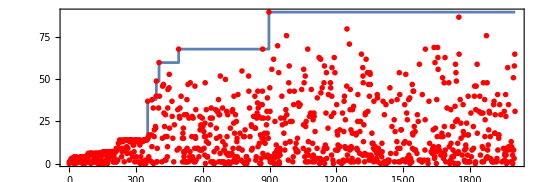

```mathematica
Show[ListStepPlot[mh[[All, 2]]], ListPlot[Min/@rh[[All, 3]], PlotHighlighting->None, PlotStyle->Red],Frame->True,AspectRatio->1/3]
```

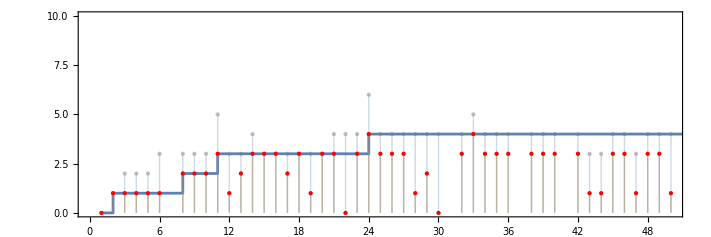

```mathematica
Show[ListStepPlot[mh[[All, 2]]], ListPlot[{Style[Catenate[MapIndexed[{First[#2],#1}&,rh[[All, 3]],{2}]],Opacity[.5,Gray],PointSize[Large]], Style[MapIndexed[{First[#2],#}&,Min/@rh[[All, 3]]],PointSize[Large],Red]},PlotHighlighting->None, Filling->Bottom],Frame->True,AspectRatio->1/3,PlotRange->{{0,50},{0,10}}]
```

```mathematica
With[{},
seq  = ResourceFunction["ProgressiveMaxPositions"][Min/@rh[[All, 3]]/.-Infinity-> 0];
Show[
 ListPlot[Style[Catenate[MapIndexed[{First[#2],#1}&,rh[[All, 3]],{2}]],Opacity[.7,Gray],PointSize[Small]], PlotHighlighting->None], 
 ListPlot[Style[Catenate[MapIndexed[{First[#2],#1}&,rh[[All, 3]],{2}]],Opacity[.7,Gray],PointSize[Small]], PlotHighlighting->None], ListPlot[Style[
MapIndexed[
If[MemberQ[seq,First[#2]],
Callout[{First[#2],Min@*Last@#1},Pane[PlotCA[PerturbedCellularAutomaton[First[#], {{1}, 0}, {200, {-50, 50}},<||>], "Trim"-> {1, 3}, ImageSize->{Automatic, 10Sqrt[1+#1[[-1, 1]]]}]],Above],
{First[#2],Min@*Last@#1}]&,rh],PointSize[.0035],Red],PlotHighlighting->None, Filling->None, FillingStyle->LightGray, PlotRange->All],
ListStepPlot[mh[[All, 2]], PlotHighlighting->None],Frame->True,AspectRatio->1/3,PlotRange->All]]
```

-Graphics-

With all base cas

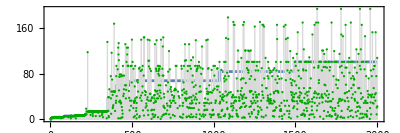

```mathematica
With[{},
seq  = ResourceFunction["ProgressiveMaxPositions"][Min/@rh[[All, 3]]/.-Infinity-> 0];
Show[
(* ListPlot[Style[Catenate[MapIndexed[{First[#2],#1}&,rh[[All, 3]],{2}]],Opacity[.7,Gray],PointSize[Small]], PlotHighlighting->None], 
 ListPlot[Style[Catenate[MapIndexed[{First[#2],#1}&,rh[[All, 3]],{2}]],Opacity[.7,Gray],PointSize[Small]], PlotHighlighting->None], ListPlot[Style[
MapIndexed[
If[MemberQ[seq,First[#2]],
Callout[{First[#2],Min@*Last@#1},Pane[PlotCA[PerturbedCellularAutomaton[First[#], {{1}, 0}, {200, {-50, 50}},<||>], "Trim"-> {1, 3}, ImageSize->{Automatic, 10Sqrt[1+#1[[-1, 1]]]}]],Above],
{First[#2],Min@*Last@#1}]&,rh],PointSize[.0035],Red],PlotHighlighting->None, Filling->None, FillingStyle->LightGray, PlotRange->All],*)
ListStepPlot[mh[[All, 2]], PlotHighlighting->None],
ListPlot[Style[rh[[All, -1, 1]], Darker[Green], PointSize[.004]], PlotHighlighting->None, Filling->Bottom, FillingStyle->LightGray],
Frame->True,AspectRatio->1/3,PlotRange->All]]
```

Other options, with no red and green highlighted

```mathematica
With[{},
seq  = ResourceFunction["ProgressiveMaxPositions"][Min/@rh[[All, 3]]/.-Infinity-> 0];
Show[
 ListPlot[Style[Catenate[MapIndexed[{First[#2],#1}&,rh[[All, 3]],{2}]],Opacity[.7,Gray],PointSize[Small]], PlotHighlighting->None], 
 ListPlot[Style[Catenate[MapIndexed[{First[#2],#1}&,rh[[All, 3]],{2}]],Opacity[.7,Gray],PointSize[Small]], PlotHighlighting->None], 
ListPlot[Style[rh[[All, -1, 1]], Darker[Green, .2], PointSize[.0035]], PlotHighlighting->None(*, Filling->Bottom, FillingStyle->LightGray*)],ListPlot[Style[
MapIndexed[
If[MemberQ[seq,First[#2]],
Callout[{First[#2],Min@*Last@#1},Pane[PlotCA[PerturbedCellularAutomaton[First[#], {{1}, 0}, {200, {-50, 50}},<||>], "Trim"-> {1, 3}, ImageSize->{Automatic, 10Sqrt[1+#1[[-1, 1]]]}]],Above],
{First[#2],Min@*Last@#1}]&,rh],PointSize[.0035],Red],PlotHighlighting->None, Filling->None, FillingStyle->LightGray, PlotRange->All],
ListStepPlot[mh[[All, 2]], PlotHighlighting->None],
Frame->True,AspectRatio->1/3,PlotRange->All]]
```

-Graphics-

#### Lifetime on cands

TODO: Run this for 400

```mathematica
allpertscands = Module[{init = {{1}, 0}, txspec = {200, {-110, 110}}},
Map[
Function[rule,  allperts[rule, init, txspec]], cands]];
```

```mathematica
ltscands = Module[{init = {{1}, 0}, txspec = {200, {-110, 110}}},
ParallelMap[
Function[{rule, aps}, TestCALifeTime[PerturbedCellularAutomaton[rule, init, txspec, #, "ReturnPerturbations"->False]]&/@ aps]@@#&, Transpose[{cands, allpertscands}]]];
```

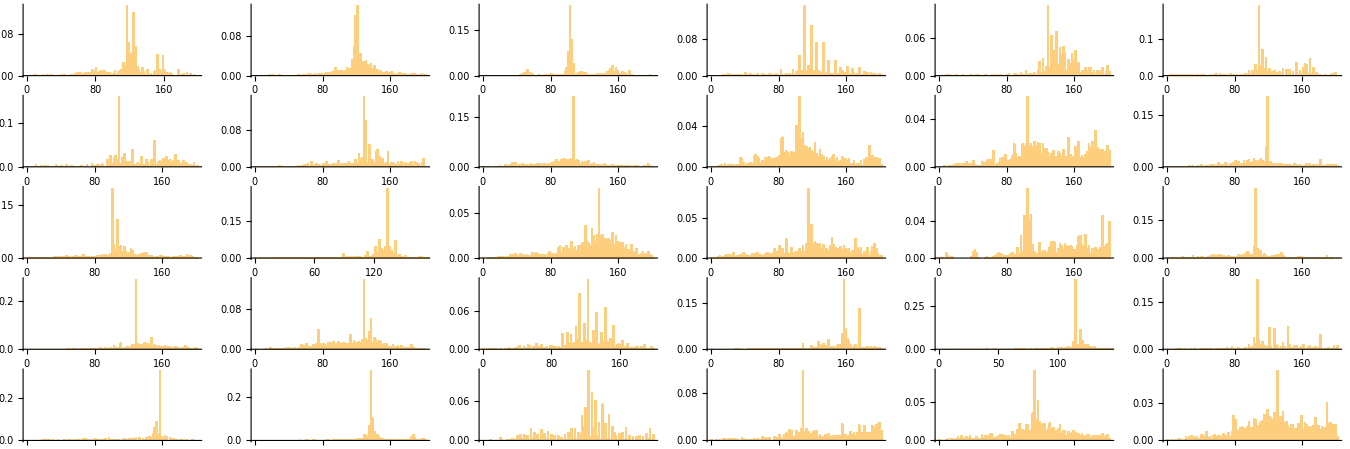

```mathematica
Histogram[#, 100, "Probability",AspectRatio->.4]&/@ ltscands //GraphicsGrid[Partition[#,6]]&
```

## More honest therapy sensitivity

```mathematica
GraphicsRow[Reverse@Module[{ru = {299459058088077823758143088095350287424,4,1},init = {{1}, 0},txspec =  {105, {-110, 110}}, aps, pca, ca, lt},
ca = PerturbedCellularAutomaton[ru, init, txspec, {}];
{TherapySensitivityPlot[ru, init, txspec,<|{23,111}->2|>, "MaxLength"->105, Mesh->True, MeshStyle->Opacity[.1]],ArrayPlot[Table[Table[x,4],{x,1,101}], ColorFunctionScaling->True,MeshStyle->Opacity[0.1], ColorFunction->(If[#< .225, LightGray,If[#==1,Darker[Red],
Blend[Reverse@{Orange, Lighter[Orange, .2], Lighter[Orange, .4],  Yellow},#-.225]]]&), Mesh->{True, False}]}]]
```

-Graphics-

```mathematica
GraphicsRow[Module[{ru = {299459058088077823758143088095350287424,4,1},init = {{1}, 0},txspec =  {105, {-110, 110}}, aps, pca, ca},
ca = PerturbedCellularAutomaton[ru, init, txspec, {}];
TherapySensitivityPlot[ru, init, txspec,#,"MaxLength"->105, Mesh->None ]&/@ (allperts[ca][[441;;450]] )]]
```

-Graphics-

## Clinical Trial Include?

```mathematica
KeyValueMap[Labeled[#1,Text[#2]]&,ReverseSort[Counts[PlotCA[PerturbedCellularAutomaton[#,{{1},0},{102,{-200,200}},<|{10,203}->0,{34,197}->3|>],ImageSize->{Automatic,150}]&/@quickneutral[{299459058088077823758143088095350287424,4,1}]]]]
```

{-Graphics-16,-Graphics-4,-Graphics-4,-Graphics-4,-Graphics-4,-Graphics-4,-Graphics-4,-Graphics-1,-Graphics-1,-Graphics-1,-Graphics-1,-Graphics-1,-Graphics-1,-Graphics-1,-Graphics-1,-Graphics-1,-Graphics-1,-Graphics-1,-Graphics-1,-Graphics-1,-Graphics-1,-Graphics-1,-Graphics-1,-Graphics-1,-Graphics-1,-Graphics-1,-Graphics-1,-Graphics-1,-Graphics-1,-Graphics-1,-Graphics-1}